# Least Squares Approximation for Linear Regressions SCIMATH203: Linear Algebra - Project

## Robin Martin van den Berg 20 May 2022

## 1) Simple Example: Small Sample of Integers

```mathematica
(* We begin by defining a set of 5 values for our x and y variables: *)
x={5,11,7,9,12};
y={21,43,32,36,45};
```

```mathematica
(* We then form the augmented matrix [A y] and row reduce it to see if it is consistent (and this solvable for B0 and B1): *)
Ay = Transpose[{Table[1,{Length[x]}],x,y}];
MatrixForm[RowReduce[Ay]]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
0 | 0 | 0
0 | 0 | 0)

```mathematica
(* The 3rd line indicates we need: 0*B0 + 0*B1 = 1 which is not possible. Thus the system is inconsistent. *)
(* We can approximate a solution using Least Squares. Letting A = [1 x] we can solve the normal equations for B^=(A^tA)^-1A^ty*)
A= Transpose[{Table[1,{Length[x]}],x}];
MatrixForm[Transpose[A].A]
MatrixForm[Inverse[Transpose[A].A]]
Bhat=Inverse[Transpose[A].A].Transpose[A].Transpose[y] 
N[Bhat]
```

(5 | 44
44 | 420)

(105/41 | -11/41
-11/41 | 5/164)

{259/41,271/82}

{6.31707,3.30488}

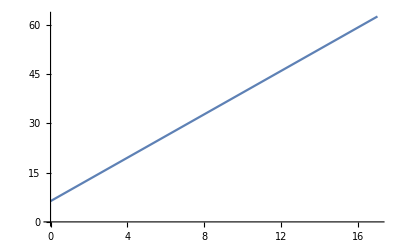

```mathematica
(* Now that we have B^0 and B^1 we can define and plot the line for our linear regression model: *)
Bhat0=Bhat[[1]];
Bhat1=Bhat[[2]];
f1[x_]:=Bhat0 + Bhat1 *x
P11=Plot[f1[t],{t,Min[x]-5,Max[x]+5},AxesOrigin->{0,0}]
```

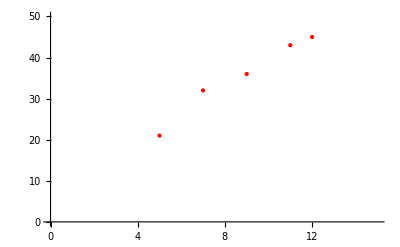

```mathematica
(* We can also plot the data points: *)
P12=ListPlot[Transpose[{x,y}],PlotStyle->{Red,PointSize[Large]},PlotRange->{{0,15},{0,50}},AxesOrigin->{0,0}]
```

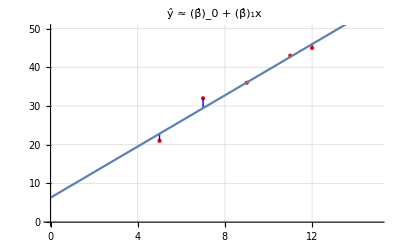

```mathematica
(* This shows the data and the model in one graph: *)
Show[P12,Graphics[{Blue,Thin,Map[Line[{#}]&,Transpose[{Transpose[{x,f1[x]}],Transpose[{x,y}]}]]}],P11,GridLines->Automatic,PlotRange->{{0,15},{0,50}},AxesOrigin->{0,0},PlotLabel-> "ŷ ≈ (β̂)_0 + (β̂)_1x"]
```

```mathematica
(* We can also calculate the Norm and Least Squares Error: *)
norm = Norm[y-A.Bhat]
error = √Total[(y-f1[x])^2]
norm==error
```

√(449/41)

√(449/41)

True

## 2) Moderate Example: Larger Numerical Sample

```mathematica
(* We begin by defining a set of 100 values for our x variables: *)
x=RandomReal[{0,100},100]
```

{63.7946,11.9634,4.26299,16.9483,32.4669,44.1976,92.48,68.461,63.564,11.577,70.2278,89.9931,61.9871,7.8865,52.8716,13.2804,81.4789,14.6032,61.3772,92.7472,54.2042,45.7971,41.9042,2.3184,29.7879,41.5624,64.6826,58.3252,24.7508,84.9299,14.5406,33.4532,97.372,64.6163,99.5592,63.3457,41.5059,80.9369,78.1727,3.44224,78.8506,48.6601,14.7287,52.8687,65.5542,52.3301,81.9291,66.3524,55.446,57.2239,77.1626,46.2123,99.1096,36.2291,17.7521,0.469849,53.5038,99.9012,0.40816,90.7202,78.1164,90.0744,50.0511,68.304,5.82963,44.7367,85.0558,71.5489,82.3825,49.8304,31.6772,98.9592,40.4504,52.5761,5.21033,74.2805,19.3856,16.9236,54.0007,30.2241,25.4812,72.5755,94.2624,25.6353,21.7959,39.3116,74.7,40.2375,50.7399,39.7171,87.3883,60.7618,4.22864,43.0338,85.6611,45.5462,79.2021,4.2897,85.7507,31.7631}

```mathematica
(* Then we define a 100 values for the y variable that is related to the varibale x in the following way: *)
y=4x-6+RandomReal[{-100,100},{Length[x]}]
```

{254.239,14.6482,-20.2645,121.802,109.497,218.753,429.537,233.262,186.757,44.516,233.154,292.222,252.854,89.1675,161.628,119.558,360.371,-9.82446,257.181,397.144,132.306,97.3998,146.367,-83.5913,167.108,236.338,160.305,204.791,123.756,409.02,143.791,92.6328,373.782,174.109,399.534,237.568,158.477,344.659,367.286,-72.2058,395.181,155.497,4.88949,195.769,240.849,265.819,243.214,308.66,130.204,221.17,318.038,265.063,341.629,132.194,11.0703,-67.144,201.512,411.952,5.88205,382.862,331.172,349.562,171.88,240.098,-18.4467,120.156,420.879,297.981,397.053,271.989,62.8415,312.612,181.229,116.361,102.68,368.17,87.4158,111.554,151.607,158.742,125.585,218.469,386.654,68.0663,124.24,164.643,199.799,176.016,111.626,183.212,320.365,137.39,-22.2488,209.32,382.583,272.618,391.938,-36.8446,332.728,26.9918}

```mathematica
(* We then form the augmented matrix [A y] and row reduce it to see if it is consistent (and this solvable for B0 and B1): *)
Ay = Transpose[{Table[1,{Length[x]}],x,y}];
MatrixForm[RowReduce[Ay]]
```

(1 | 0. | 0.
0 | 1 | 0.
0 | 0 | 1
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
(* The 3rd line indicates we need: 0*B0 + 0*B1 = 1 which is not possible. Thus the system is inconsistent. *)
(* We can approximate a solution using Least Squares. Letting A = [1 x] we can solve the normal equations for B^=(A^tA)^-1A^ty*)
A= Transpose[{Table[1,{Length[x]}],x}];
Bhat=Inverse[Transpose[A].A].Transpose[A].Transpose[y]
```

{-14.6564,4.12539}

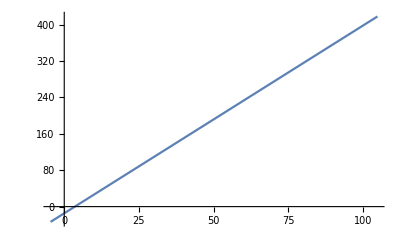

```mathematica
(* Now that we have B^0 and B^1 we can define and plot the line for our linear regression model: *)
Bhat0=Bhat[[1]];
Bhat1=Bhat[[2]];
f2[x_]:=Bhat0 + Bhat1 *x
P21=Plot[f1[t],{t,Min[x]-5,Max[x]+5},AxesOrigin->{0,0}]
```

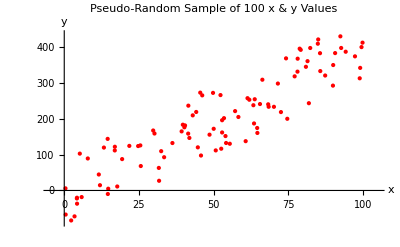

```mathematica
(* We can also plot the data points: *)
P22=ListPlot[Transpose[{x,y}],PlotStyle->{Red,PointSize[Large]},PlotRange->{{Min[x]-5,Max[x]+5},{Min[y]-5,Max[y]+5}},AxesLabel-> {"x","y"},AxesOrigin->{0,0},PlotLabel-> "Pseudo-Random Sample of 100 x & y Values"]
```

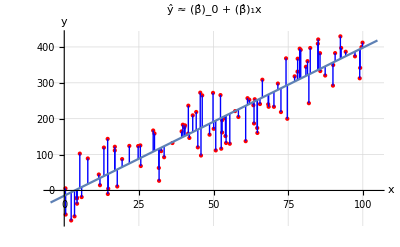

```mathematica
(* This shows the data and the model in one graph: *)
Show[P22,Graphics[{Blue,Thin,Map[Line[{#}]&,Transpose[{Transpose[{x,f2[x]}],Transpose[{x,y}]}]]}],P21,GridLines->Automatic,PlotRange->{{Min[x]-5,Max[x]+5},{Min[y]-5,Max[y]+5}},AxesLabel-> {"x","y"},AxesOrigin->{0,0},PlotLabel-> "ŷ ≈ (β̂)_0 + (β̂)_1x"]
```

```mathematica
(* We can also calculate the Norm and Least Squares Error: *)
norm = Norm[y-A.Bhat]
error = √Total[(y-f2[x])^2]
norm==error
```

540.959

540.959

True

## 3) Extra Complex Example: 2 Independent Variables

```mathematica
(* We begin by defining a set of 100 values for our x1 variable: *)
x1=RandomReal[{0,100},100]
```

{26.7137,20.6946,29.6189,67.0138,44.2965,20.2195,52.3944,19.7936,89.1575,42.9373,96.3947,69.8601,35.6094,19.5914,37.512,40.3831,1.10576,91.8671,99.0019,79.8337,93.9013,85.2631,66.4064,4.2014,18.2755,52.2557,4.92417,91.6089,53.5057,97.597,41.3583,25.9061,0.598016,95.8833,35.6742,30.4666,94.2297,14.3891,63.3904,84.9456,17.5617,0.755005,73.2919,31.0361,37.4101,28.2522,76.0374,61.4387,44.1862,9.99673,33.781,90.11,73.0639,70.8223,21.8157,19.9926,49.185,38.7511,83.3382,94.7539,6.59678,25.8812,63.9532,16.2099,9.25859,80.1074,21.7172,36.3332,99.6278,79.9956,56.9323,50.848,0.639434,72.5068,65.3413,90.4077,79.2268,58.7038,42.7826,9.5557,3.42958,19.5216,75.6549,3.34264,82.0056,62.6471,85.4024,90.546,24.4082,31.6951,30.0148,29.2782,94.4072,70.4862,31.821,26.4397,49.7873,57.2514,85.2715,41.1864}

```mathematica
(* We begin by defining a set of 100 values for our x2 variable: *)
x2=RandomReal[{-100,100},100]
```

{98.7548,61.7902,43.904,41.7791,-76.0575,95.326,0.739743,57.8614,-82.8809,33.2257,-72.8889,74.2264,-47.7133,-40.5166,-16.5265,-92.8902,37.8321,-49.5473,-80.4012,24.726,36.5492,99.6661,-26.3797,-11.3773,18.7339,13.863,-54.9141,37.6496,-94.5471,-55.2161,92.3743,98.3655,-61.5515,-67.1456,-50.3499,-40.0871,99.6665,53.4802,23.6523,21.9674,-23.7448,-52.4925,-70.104,46.0536,-14.6238,18.4378,8.79859,92.0119,-17.9333,-73.009,-12.8976,-98.168,18.1884,4.00103,-14.6469,-27.0446,43.4673,-82.2118,-70.5905,86.2806,63.418,-17.9308,-77.3668,-27.6507,-12.7047,59.7465,-10.4172,32.4193,22.4272,91.9269,-23.0129,92.8374,-70.06,-18.2894,4.92268,-47.9843,-38.3552,-2.50025,79.9547,30.5639,-25.4612,31.2626,52.8497,-3.70756,-36.7954,-12.3482,-61.0961,19.8662,-20.7817,-57.0597,-22.676,-40.0749,-50.9796,-69.8573,72.4444,-73.646,82.5744,-68.3716,76.0899,-61.5387}

```mathematica
(* Then we define a 100 values for the y variable that is related to the varibale x in the following way: *)
y=5x1-3x2+7-RandomReal[{-100,100},100]
```

{-86.9756,14.4449,9.59915,132.003,525.254,-257.76,245.624,29.7621,663.829,200.164,776.008,159.183,273.577,156.429,280.564,545.073,-138.406,572.561,692.614,373.765,308.349,183.148,505.776,148.705,-22.3167,318.257,128.136,428.307,552.212,684.518,-92.3972,-96.9312,227.753,655.623,359.357,225.677,124.766,-83.747,348.118,385.978,235.254,118.874,593.208,79.5684,305.712,46.5984,294.127,-54.7203,206.822,373.617,239.6,757.287,218.379,371.049,188.053,118.918,80.6529,489.923,541.334,173.065,-210.268,267.54,628.45,167.496,20.3205,203.777,149.924,167.048,490.8,146.017,391.201,26.0951,257.118,376.54,258.54,671.341,555.033,271.83,14.5123,5.66977,20.33,-79.6446,199.706,-48.3698,586.378,386.209,710.416,399.756,167.896,292.186,199.181,309.062,591.502,500.998,16.3919,443.554,-42.9259,505.446,288.387,431.809}

```mathematica
(* We then form the augmented matrix [A y] and row reduce it to see if it is consistent (and this solvable for B0 B1 and B2): *)
Ay = Transpose[{Table[1,{Length[x1]}],x1,x2,y}];
MatrixForm[RowReduce[Ay]]
```

(1 | 0. | 0. | 0.
0 | 1 | 0. | 0.
0 | 0 | 1 | 0.
0 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
(* The 4th line indicates we need: 0*B0 + 0*B1 + 0*B3 = 1 which is not possible. Thus the system is inconsistent. *)
(* We can approximate using Least Squares. Letting A = [1 x1 x2] we can solve the normal equations for B^=(A^tA)^-1A^ty*)
A= Transpose[{Table[1,{Length[x1]}],x1, x2}];
Bhat=Inverse[Transpose[A].A].Transpose[A].Transpose[y]
```

{9.91383,5.01971,-3.02953}

```mathematica
(* Now that we have B^0 and B^1 we can define and plot the line for our linear regression model: *)
Bhat0=Bhat[[1]];
Bhat1=Bhat[[2]];
Bhat2=Bhat[[3]];
f3[x_,y_]:=Bhat0 + Bhat1 *x + Bhat2 *y
P31=Plot3D[f3[t,u],{t,Min[x1]-5,Max[x1]+5},{u,Min[x2]-5,Max[x2]+5},AxesOrigin->{0,0,0},PlotStyle->Yellow]
```

-Graphics3D-

```mathematica
(* We can also plot the data points: *)
P32=ListPointPlot3D[Transpose[{x1,x2,y}],PlotStyle->{Red,PointSize[Large]},PlotRange->{{Min[x1]-5,Max[x1]+5},{Min[x2]-5,Max[x2]+5},{Min[y]-5,Max[y]+5}},AxesLabel-> {"x1","x2","y"},AxesOrigin->{0,0,0},PlotLabel-> "Pseudo-Random Sample of 100 x_1, x_2 & y Values"]
```

-Graphics3D-

```mathematica
Show[P32,P31,GridLines->Automatic,PlotRange->Automatic,AxesOrigin->{0,0,0},AxesLabel-> {"x1","x2","y"},PlotLabel-> "ŷ ≈ (β̂)_0 + (β̂)_1x_1 + (β̂)_2x_2"]
```

-Graphics3D-

```mathematica
norm = Norm[y-A.Bhat]
error = √Total[(y-f3[x1,x2])^2]
norm==error
```

577.539

577.539

True